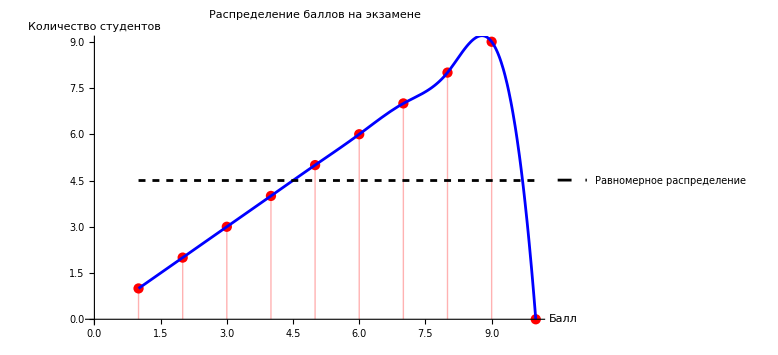

```mathematica
(*вставьте сюда "дата" через запятую !*)
resultMath = {1, 2, 3, 4, 5, 6, 7, 8, 9, 0};

data=Table[{i,resultMath[[i]]},{i,Length[resultMath]}];

meanValue=Mean[resultMath];

smooth=Interpolation[data,Method->"Spline"];

Show[ListPlot[data,PlotStyle->Red,Filling->Axis,PlotLabel->"Распределение баллов на экзамене",AxesLabel->{"Балл","Количество студентов"},ImageSize->Large],Plot[smooth[x],{x,1,Length[resultMath]},PlotStyle->Blue],Plot[meanValue,{x,1,Length[resultMath]},PlotStyle->{Black,Dashed},PlotLegends->{"Равномерное распределение"}]]
```

```mathematica
ъ
```